```mathematica
ds = Import["/home/flexagoon/Documents/Events/Public/Olympiads/DANO/2023/Хакатон/holidays.csv", "Dataset", "HeaderLines"->1]
```

Dataset[<>]

```mathematica
{ds[Select[#"temperature">=10&]][Counts, "service"] // ReverseSort,
ds[Select[#"temperature"<10&]][Counts, "service"] // ReverseSort}
```

{,}

```mathematica
Table[Keys[Normal[ReverseSort[ds[Select[#"temperature">=x&]][Counts, "service"]]]][[6]],{x,-20,20}]
```

{Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Вкусвилл,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Красота,Книги,Красота}

```mathematica
Length[ds[Select[#"temperature"==0&]]] / Length[ds]
Length[ds[Select[#"temperature"==1&]]] / Length[ds]
```

879/24721

1057/24721

```mathematica
temps = DeleteCases[ds[All, "temperature"] // Normal //DeleteDuplicates, ""];
prop[val_]:=Length[ds[Select[#"temperature"==val&]]] / Length[ds]
tempWeights = AssociationMap[prop] @ temps
```

<|-18→85/24721,1→1057/24721,-2→654/24721,0→879/24721,-14→220/24721,2→795/24721,22→471/24721,31→318/24721,10→603/24721,9→566/24721,17→478/24721,-13→165/24721,4→433/24721,12→607/24721,6→473/24721,-16→132/24721,26→401/24721,18→449/24721,19→469/24721,25→525/24721,15→499/24721,-8→555/24721,14→668/24721,34→56/24721,3→640/24721,28→429/24721,5→455/24721,29→455/24721,7→8/419,-15→154/24721,21→418/24721,-1→657/24721,-20→74/24721,11→540/24721,-5→719/24721,16→485/24721,-3→644/24721,-10→223/24721,-6→660/24721,27→447/24721,13→9/419,-7→517/24721,-11→267/24721,23→505/24721,-17→113/24721,24→461/24721,30→343/24721,20→418/24721,-4→725/24721,-22→44/24721,-12→206/24721,8→445/24721,-21→39/24721,-9→284/24721,-24→12/24721,-28→4/24721,-19→101/24721,32→206/24721,-27→5/24721,-46→2/24721,-39→3/24721,-26→8/24721,-32→8/24721,35→30/24721,33→82/24721,38→9/24721,-36→7/24721,-38→2/24721,-29→7/24721,-23→25/24721,-25→7/24721,36→5/24721,-30→5/24721,-37→4/24721,-34→2/24721,37→4/24721,39→1/24721|>

```mathematica
removeEmptyKeys[assoc_Association]:=KeySelect[assoc,KeyExistsQ[assoc,#]&&#=!=""&]
```

```mathematica
tempData[service_] := Module[{vals,temps,weights,out},
vals = removeEmptyKeys[Normal[ds[Select[#"service"==service&]][Counts, "temperature"]]];
temps = vals // Keys;
weights = AssociationMap[prop, temps];
out = MapThread[Divide, {vals,weights}];
out // KeySort
]
```

```mathematica
rawTempData[service_]:=removeEmptyKeys[Normal@ds[Select[#"sex"=="F"&]][Select[#"service"==service&]][Counts, "temperature"]]
```

```mathematica
homeTempData = Module[{vals,temps,weights,out},
vals = removeEmptyKeys[Normal[ds[Select[{"Вкусвилл","Игры"}~ContainsAll~{#"service"}&]][Counts, "temperature"]]];
temps = vals // Keys;
weights = AssociationMap[prop, temps];
out = MapThread[Divide, {vals,weights}];
out // KeySort
];
rawHomeTempData =removeEmptyKeys[Normal@ds[Select[{"Вкусвилл","Игры"}~ContainsNone~{#"service"}&]][Counts, "temperature"]];
streetTempData = Module[{vals,temps,weights,out},
vals = removeEmptyKeys[Normal[ds[Select[{"Вкусвилл","Игры"}~ContainsNone~{#"service"}&]][Counts, "temperature"]]];
temps = vals // Keys;
weights = AssociationMap[prop, temps];
out = MapThread[Divide, {vals,weights}];
out // KeySort
];
rawStreetTempData =removeEmptyKeys[Normal@ds[Select[{"Вкусвилл","Игры"}~ContainsNone~{#"service"}&]][Counts, "temperature"]];
```

```mathematica
MinMax[Keys@homeTempData]
MinMax[Keys@streetTempData]
```

{-46,38}

{-46,39}

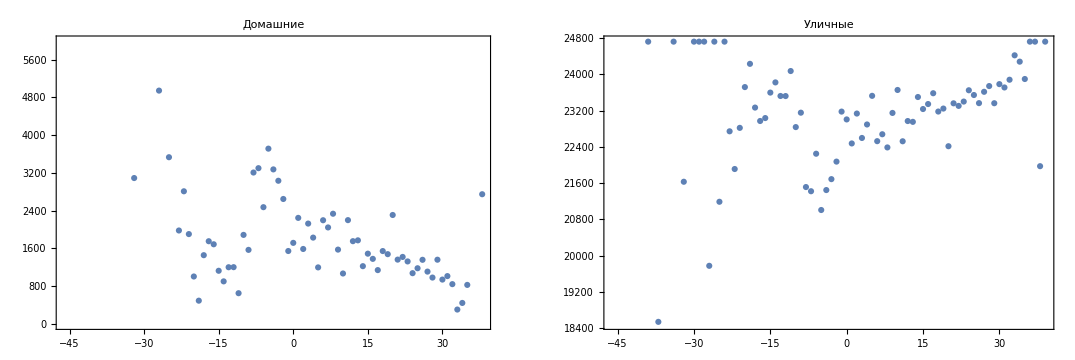

```mathematica
GraphicsRow[{
homeTempData//ListPlot[#, PlotLabel->"Домашние", Frame -> True]&,
streetTempData//ListPlot[#, PlotLabel->"Уличные", Frame -> True]&
}]
```

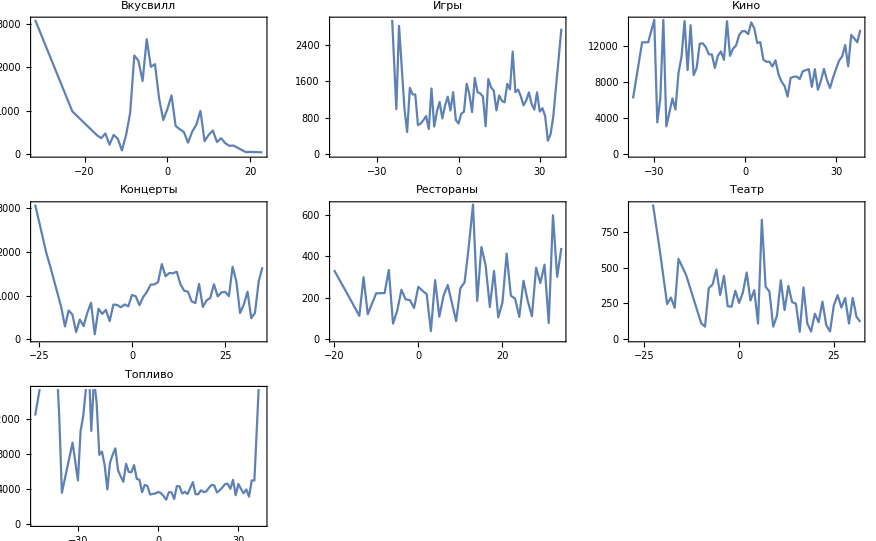

```mathematica
GraphicsGrid[{
{
tempData["Вкусвилл"]//ListLinePlot[#, PlotLabel->"Вкусвилл", Frame -> True]&,
tempData["Игры"]     // ListLinePlot[#, PlotLabel->"Игры", Frame -> True]&,
tempData["Кино"]     // ListLinePlot[#, PlotLabel->"Кино", Frame -> True]&
},
{
tempData["Концерты"]     // ListLinePlot[#, PlotLabel->"Концерты", Frame -> True]&,
tempData["Рестораны"]     // ListLinePlot[#, PlotLabel->"Рестораны", Frame -> True]&,
tempData["Театр"]     // ListLinePlot[#, PlotLabel->"Театр", Frame -> True]&
},
{
tempData["Топливо"]     // ListLinePlot[#, PlotLabel->"Топливо", Frame -> True]&
}
}]
```

```mathematica
tempData["Вкусвилл"][[1]] // KeySort
```

MapThread::mptd: Object <|-2→654/24721,0→879/24721,-8→555/24721,11→540/24721,2→795/24721,-7→517/24721,1→1057/24721,-4→725/24721,-5→719/24721,-3→644/24721,-6→660/24721,4→433/24721,8→445/24721,-10→223/24721,15→499/24721,3→640/24721,10→603/24721,7→8/419,-1→657/24721,-12→206/24721,-17→113/24721,-23→25/24721,12→607/24721,16→485/24721,6→473/24721,5→455/24721,-9→284/24721,14→668/24721,13→9/419,-13→165/24721,9→566/24721,-15→154/24721,20→418/24721,-16→132/24721,19→469/24721,-14→220/24721,-11→267/24721,-32→8/24721,23→505/24721|> at position {2, 2} in MapThread[Divide,{{-2→34,0→37,-8→51,11→12,2→21,-7→45,1→58,-4→59,-5→77,-3→54,«29»},<|-2→654/24721,0→879/24721,-8→555/24721,11→540/24721,2→795/24721,-7→517/24721,1→1057/24721,-4→725/24721,-5→719/24721,-3→644/24721,-6→660/24721,4→433/24721,8→445/24721,-10→223/24721,15→499/24721,3→640/24721,10→603/24721,7→8/419,-1→657/24721,-12→206/24721,-17→113/24721,-23→25/24721,12→607/24721,16→485/24721,6→473/24721,5→455/24721,-9→284/24721,14→668/24721,13→9/419,-13→165/24721,9→566/24721,-15→154/24721,20→418/24721,-16→132/24721,19→469/24721,-14→220/24721,-11→267/24721,-32→8/24721,23→505/24721|>}] has only 0 of required 1 dimensions.

KeySort::invrl: The argument Divide is not a valid Association or a list of rules.

KeySort[Divide]

```mathematica
bc[data_]:=BarChart[KeySort@data, ChartLabels->Normal[Keys@KeySort[data]], ChartStyle->"DarkRainbow"]
d = removeEmptyKeys[Normal@ds[GroupBy["rain"], Counts, "service"]];
BarChart[{Values@d[[1]],Values@d[[2]]}];
PairedBarChart[d[[1]],d[[2]]]
```

-Graphics-

```mathematica
ds[Select[#"service"=="Топливо"&]][Counts,"rain"]
```

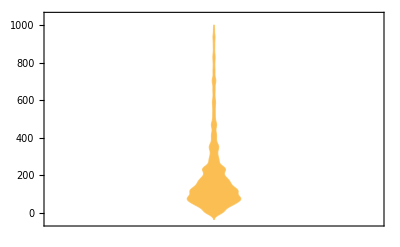

```mathematica
ds[Select[#"price"<1000&]][DistributionChart,"price"]
```

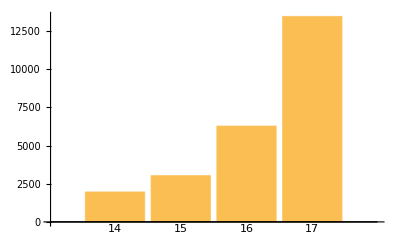

```mathematica
ds[Counts,"age"] //KeySort
BarChart[%,ChartLabels->{14,15,16,17}]
```

```mathematica
ds[Trend,"price"]
```

Modal[{282,174,183,263,284,1898,5326,0,35,1199,164,59,422,117,1385,141,136,131,82,516,1063,150,352,211,2029,155,70,14,3879,716,359,117,386,117,3031,6119,178,44,35,305,4,89,44,113,4793,70,59,178,438,1484,38,3,176,0,18,2412,164,1680,117,35,469,117,211,117,939,397,235,352,134,998,211,164,2,117,164,136,12594,188,141,253,35,47,24557,352,164,188,92,942,7004,1913,3895,235,63,0,718,141,164,35,93,293,59,493,47,1408,23,164,89,575,235,84,1314,117,821,117,117,7429,10096,23,1513,80,0,52,47,0,23,70,47,0,61,162,176,164,47,94,10325,131,469,117,117,169,352,2372,13772,94,160,154,70,0,7,235,68,82,289,0,217,329,23,23,82,160,6394,1725,329,82,141}]
 |  |  |  |

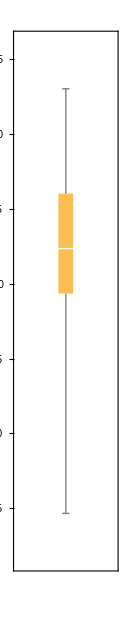
```mathematica
-Graphics--Graphics-
```

```mathematica
hprop[val_]:=Length[ds[Select[#"is_holiday"==val&]]] / Length[ds]
homeHolidayData = Module[{vals,temps,weights,out},
vals = removeEmptyKeys[Normal[ds[Select[{"Вкусвилл","Игры"}~ContainsAll~{#"service"}&]][Counts, "is_holiday"]]];
temps = vals // Keys;
weights = AssociationMap[hprop, temps];
out = MapThread[Divide, {vals,weights}];
out // KeySort
];
streetHolidayData = Module[{vals,temps,weights,out},
vals = removeEmptyKeys[Normal[ds[Select[{"Вкусвилл","Игры"}~ContainsNone~{#"service"}&]][Counts, "is_holiday"]]];
temps = vals // Keys;
weights = AssociationMap[hprop, temps];
out = MapThread[Divide, {vals,weights}];
out // KeySort
];
rawHomeHolidayData =Normal@ds[Select[{"Вкусвилл","Игры"}~ContainsAll~{#"service"}&]][Counts, "is_holiday"];
rawStreetHolidayData =Normal@ds[Select[{"Вкусвилл","Игры"}~ContainsNone~{#"service"}&]][Counts, "is_holiday"];
```

```mathematica
GraphicsRow[
{
rawStreetHolidayData//PieChart[#,ChartLabels->{"Выходной","Нет","Праздник","Перед праздником"}]&,
rawHomeHolidayData // PieChart[#,ChartLabels->{"Нет","Выходной","Праздник","Перед праздником"}]&
}
]
```

```mathematica
rawHomeHolidayData // Dataset - 1824
rawStreetHolidayData // Dataset - 22897
```

```mathematica
rawStreetHolidayData
```

<|3→7516,0→9460,1→5604,2→317|>

```mathematica
homeData = ds[Select[{"Вкусвилл","Игры"}~ContainsAll~{#"service"}&]];
streetData = ds[Select[{"Кино","Театр","Цветы","Топливо","Концерты","Рестораны"}~ContainsAll~{#"service"}&]];
```

```mathematica
ds[Counts,"sex"]
```

```mathematica
ds[Select[#"sex"=="M"&]][Counts,"service"] // ReverseSort
ds[Select[#"sex"=="F"&]][Counts,"service"] // ReverseSort
```

```mathematica
ds[Counts,"service"] // ReverseSort
ds  // Length
```

24721